```mathematica
M[sigma_] = {{sigma+3, 4}, {-9/4, sigma-3}}
```

{{4,4},{-9/4,-2}}

```mathematica
M[sigma]//MatrixForm
```

(4 | 4
-9/4 | -2)

```mathematica
x'[t] = (sigma+3)*x+4y
```

4 x+4 y

```mathematica
sigma = 0
```

0

```mathematica
x'[t]
```

4 x+4 y

```mathematica
Unset[sigma]
```

```mathematica
y'[t]=-(9/4)*x+(sigma-3)y
```

-(9 x)/4+(-3+sigma) y

```mathematica
x[0]=x0
```

x0

```mathematica
y[0]=y0
```

y0

```mathematica
y0
x0=0
```

y0

0

```mathematica
y0=0
```

0

```mathematica
0
sigma = 0
```

0

0

```mathematica
0
Unset[x0]
```

0

```mathematica
Unset[y0]
```

```mathematica
sol[x0_,y0_]:=DSolve[{x'[t] ==((sigma+3)*x[t]+4y[t]) , y'[t] ==(-(9/4)*x[t]+(sigma-3)y[t]), x[0]==x0,y[0]==y0},{x,y},{t}]
```

```mathematica
Unset[x0]
```

```mathematica
Unset[y0]
```

```mathematica
sigma = -1
```

-1

```mathematica
Eigenvectors[M]
```

Eigenvectors[M]

```mathematica
Unset[M[sigma_]]
```

```mathematica
M={{sigma+3, 4}, {-9/4, sigma-3}}
```

{{2,4},{-9/4,-4}}

```mathematica
Unset[sigma]
```

```mathematica
Eigenvectors[M]
```

{{-4/3,1},{0,0}}

```mathematica
Eigenvalues[M]
```

{-1,-1}

```mathematica
Inverse[M]
```

{{-4,-4},{9/4,2}}

```mathematica
M2 = {{(sigma-c*d), d^2}, {-c^2, (sigma+c*d)}}
```

{{-c d+sigma,d^2},{-c^2,c d+sigma}}

```mathematica
M2//MatrixForm
```

(-c d+sigma | d^2
-c^2 | c d+sigma)

```mathematica
Eigenvalues[M2]
Eigenvectors[M2]
```

{sigma,sigma}

{{d/c,1},{0,0}}

```mathematica
{sigma,sigma}
```

{sigma,sigma}

```mathematica
{1/2 (x-c d x+y+c d y-√(-4 x y+(-x+c d x-y-c d y)^2)),1/2 (x-c d x+y+c d y+√(-4 x y+(-x+c d x-y-c d y)^2))}
```

{1/2 (x-c d x+y+c d y-√(-4 x y+(-x+c d x-y-c d y)^2)),1/2 (x-c d x+y+c d y+√(-4 x y+(-x+c d x-y-c d y)^2))}

```mathematica
sigma = 0
```

0

```mathematica
minx=-1;
miny=-1;
maxx=1;
maxy=1;
inits =Join[Table[ {minx,y},{y,miny,maxy,0.1}],Table[ {maxx,y},{y,miny,maxy,0.1}],Table[ {x,miny},{x,minx,maxx,0.1}],Table[ {x,maxy},{x,minx,maxx,0.1}]];
```

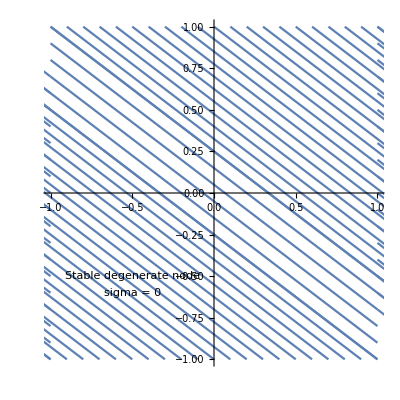

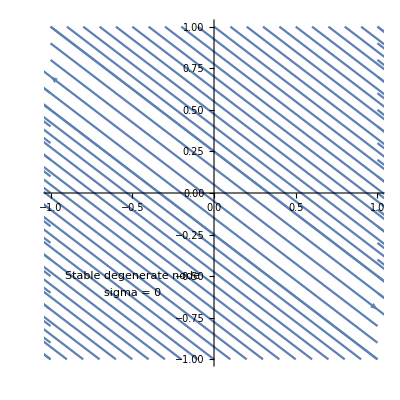

```mathematica
p0 = Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol[inits[[i,1]],inits[[i,2]]]],{t,0,10},PlotRange->{{minx,maxx},{miny,maxy}}],{i,Length[inits]}], text, text2]
(p0//Normal)/.Line[x_]:>{Arrowheads[{0,0.05,0}],Arrow[x]}
```

```mathematica
sol[x0,y0]
```

DSolve::deqn: Equation or list of equations expected instead of True in the first argument {4 x+4 y==-4 x[t]-4 y[t],-(9 x)/4-2 y==(9 x[t])/4+2 y[t],True,True}.

DSolve[{4 x+4 y==-4 x[t]-4 y[t],-(9 x)/4-2 y==(9 x[t])/4+2 y[t],True,True},{x,y},{t}]

```mathematica
Evaluate[{x[t],y[t]}/.sol[inits[[1,1]],inits[[1,2]]]]
```

DSolve::dvnoarg: The function x appears with no arguments.

ReplaceAll::reps: {DSolve[{4 x+4 y==-4 x[t]-4 y[t],-(9 x)/4-2 y==(9 x[t])/4+2 y[t],x0==-1,y0==-1.},{x,y},{t}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{x[t],y[t]}/.DSolve[{4 x+4 y==-4 x[t]-4 y[t],-(9 x)/4-2 y==(9 x[t])/4+2 y[t],x0==-1,y0==-1.},{x,y},{t}]

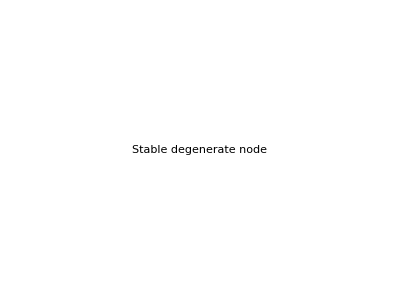

-Graphics-

```mathematica
text = Graphics[Text["Line of F.P", {-0.5, -0.5}]]
text2 = Graphics[Text["sigma = 0", {-0.5, -0.6}]]
```